```mathematica
Quit
```

```mathematica
Assuming[1> θc > 0,Integrate[Exp[1/x] x^2,{x,θc,1}]]
```

1/6 (4 ⅇ-ⅇ^(1/θc) θc (1+θc+2 θc^2)-ExpIntegralEi[1]+ExpIntegralEi[1/θc])

```mathematica
Assuming[1> θc > 0,Series[%2,{θc,0,4}]]
```

1/6 (4 ⅇ-ExpIntegralEi[1]+ⅇ^(1/θc) (-θc-θc^2-2 θc^3+O[θc]^5)+ⅇ^(1/θc) (θc+θc^2+2 θc^3+6 θc^4+O[θc]^5))

```mathematica
N[1/6 (4 ⅇ-ExpIntegralEi[1]+ⅈ π Floor[-Arg[θc]/(2 π)]-ⅈ π Floor[Arg[θc]/(2 π)]+ⅈ π Floor[(π+Arg[θc])/(2 π)]) /. θc-> .001]
```

1.49633

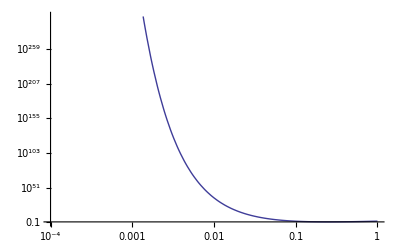

```mathematica
LogLogPlot[θc^4 Exp[1/θc],{θc,.0001,1}]
```